## Input Parameters

```mathematica
NFP=2;sigma0=0;R0=1;
ns=26;nIts=6;tol=10^-5;nLineS=3;
etabmin=0.4;etabmax=1.3;maxiterations=1500;searchpoints=500;
eR1min=0.04;eR1max=0.1;eZ1min=eR1min;eZ1max=eR1max;
eR2min=-0.02;eR2max=0.02;eZ2min=eR2min;eZ2max=eR2max;
sigmainit[t_]=0.01 Cos[NFP t];
psi31init[t_]=0.01Cos[NFP t];
psi32init[t_]=0.01Sin[NFP t];
psi33init[t_]=0.01Cos[NFP t];
psi34init[t_]=0.01Sin[NFP t];
```

## Sigma Equation

### Residual Function

```mathematica
qsresidualsigma[Dmat_,sigma_,tors_,curv_,sprime_,etab_,F0_,ns_,sigma0_]:=Module[{},
f={Dmat.sigma+sprime*(F0*(1+sigma^2+etab^4/curv^4)+2*etab^2/curv^2*tors),
(sigma//Last)-sigma0}//Flatten;
dfdsigma=Dmat-DiagonalMatrix[(sprime*F0*2*sigma)//Flatten];
dfdiota=sprime*(1+sigma^2+etab^4/curv^4);
Jacf=Append[Append[dfdsigma//Transpose,dfdiota]//Transpose,{ConstantArray[0,{1,ns-1}],1,0}//Flatten];
{f,Jacf}]
```

### Function to Solve for Sigma and F0

```mathematica
solveSigma[nIts_,tol_,nLineS_,Dmat_,sigmaI_,tors_,curv_,sprime_,ns_,sigma0_,F0init_,etab_]:=Module[{F0=F0init,sigma=sigmaI,deltaold=0},
For[i=1,i<nIts,i++,
{f1,Jacf1}=qsresidualsigma[Dmat,sigma,tors,curv,sprime,etab,F0,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
{f2,Jacf2}=qsresidualsigma[Dmat,sigma+deltay[[1 ;; ns]],tors,curv,sprime,etab,F0+deltay//Last,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2]
];
sigma=sigma+deltay[[1 ;; ns]];
F0=F0+deltay//Last;
];
{sigma,F0}//Flatten]
```

## Psi3 Equation

### Set of Equations for psi3

```mathematica
psi3MatrixA=({{-3 F0 σ[s]+(2 k'[s])/k[s], (5 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+3 α'[s], (3 k'[s])/k[s], 3/2 ((F0 ηb^2)/k[s]^2+(F0 k[s]^2 (1+σ[s]^2))/ηb^2+2 α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], F0 σ[s]-(2 k'[s])/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(3 F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-3 α'[s], (3 k'[s])/k[s]}, {-F0 σ[s]+k'[s]/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-α'[s], 0, 3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], -F0 σ[s]+k'[s]/k[s], -3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s]), 0}});
psi3MatrixB=1/(B0 c0)({{{{(B0 c0 (4 F0^3 ηb^10 k[s] σ[s]+4 F0^2 ηb^10 k'[s]+2 k[s]^10 (1+σ[s]^2) k'[s] (-ηb^2+F0 (1+σ[s]^2) α'[s])+2 k[s]^2 (2 ηb^6 k'[s]^3+5 F0 ηb^8 k'[s] α'[s])+F0 k[s]^11 (1+σ[s]^2) (4 ηb^2 σ[s]-2 F0 (σ[s]+σ[s]^3) α'[s]+(1+σ[s]^2) α''[s])+ηb^6 k[s]^3 (2 F0 σ[s] (4 k'[s]^2+9 F0 ηb^2 α'[s])-3 (k'[s] k''[s]+F0 ηb^2 α''[s]))+ηb^2 k[s]^6 (-4 (1+σ[s]^2) k'[s]^3+8 ηb^2 σ[s] α'[s] k''[s]+ηb^2 k'[s] (ηb^2-4 F0 (3+5 σ[s]^2) α'[s]+4 σ[s] α''[s]))+k[s]^5 (8 F0^3 ηb^6 σ[s]^3-4 ηb^4 σ[s] k'[s]^2 α'[s]+6 F0 ηb^6 σ[s] (F0^2+3 α'[s]^2)-ηb^6 (6 α'[s] α''[s]+F0 σ''[s]))+ηb^2 k[s]^9 (4 F0^3 σ[s]^5+6 σ[s]^3 (F0^3-F0 α'[s]^2)+σ[s] (2 F0^3+3 α'[s] (ηb^2-2 F0 α'[s]))+6 α'[s] α''[s]+F0 σ''[s]+σ[s]^2 (6 α'[s] α''[s]+F0 σ''[s]))-ηb^2 k[s]^8 (1+σ[s]^2) (2 k'[s] (F0^2+4 F0^2 σ[s]^2-α'[s]^2)-2 F0 σ[s] k''[s]+Derivative[3][k][s])+ηb^6 k[s]^4 (-2 k'[s] (F0^2+2 F0^2 σ[s]^2+α'[s]^2)-2 F0 σ[s] k''[s]+Derivative[3][k][s])+ηb^2 k[s]^7 (4 F0 σ[s]^3 (k'[s]^2+4 F0 ηb^2 α'[s])+3 k'[s] k''[s]+2 F0 ηb^2 α''[s]+σ[s]^2 (3 k'[s] k''[s]-2 F0 ηb^2 α''[s])+2 σ[s] (2 F0 k'[s]^2+ηb^2 (2 F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])))))/(2 ηb^4 k[s]^8)}}}, {{{(B0 c0 (4 F0^3 ηb^12+4 F0 ηb^8 k[s]^2 (3 k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^12 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^4 (F0^3 ηb^8 (1+2 σ[s]^2)-2 ηb^6 k'[s]^2 α'[s]+7 F0 ηb^8 α'[s]^2)+2 F0 k[s]^11 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s]^3 (10 F0 σ[s] k'[s]+k''[s])+2 ηb^2 k[s]^9 (ηb^2 σ[s] k'[s]+8 F0 σ[s] k'[s] α'[s]+8 F0 σ[s]^3 k'[s] α'[s]-4 α'[s] k''[s]-4 σ[s]^2 α'[s] k''[s]-2 (1+σ[s]^2) k'[s] α''[s])+4 ηb^4 k[s]^5 (-4 σ[s] (k'[s]^3+3 F0 ηb^2 k'[s] α'[s])+ηb^2 (2 α'[s] k''[s]+k'[s] α''[s]))-2 ηb^2 k[s]^8 (2 F0^3 ηb^2+2 F0^3 ηb^2 σ[s]^4+α'[s] (ηb^4-2 k'[s]^2+8 F0 ηb^2 α'[s])+2 σ[s]^2 (-k'[s]^2 α'[s]+2 F0 ηb^2 (F0^2+4 α'[s]^2))-2 ηb^2 σ[s] (6 α'[s] α''[s]+F0 σ''[s]))+4 ηb^4 k[s]^7 (-4 F0^2 σ[s]^3 k'[s]+F0 k''[s]+F0 σ[s]^2 k''[s]-σ[s] (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))+ηb^4 k[s]^6 (-3 F0 ηb^4+4 F0 (-3+σ[s]^2) k'[s]^2+12 σ[s] k'[s] k''[s]+2 ηb^2 (-2 α'[s] (F0^2+2 F0^2 σ[s]^2+α'[s]^2)+4 F0 σ[s] α''[s]+Derivative[3][α][s]))-ηb^2 k[s]^10 (24 F0^2 σ[s]^4 α'[s]-8 F0 σ[s] α''[s]-8 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (3 F0 ηb^2+36 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))))/(4 ηb^4 k[s]^9)}}}, {{{(B0 c0 (-4 F0^2 ηb^10 k'[s]+2 F0 k[s]^10 (1+σ[s]^2)^2 k'[s] α'[s]-ηb^2 k[s]^6 k'[s] (ηb^4+4 (1+σ[s]^2) k'[s]^2+8 F0 ηb^2 (1+σ[s]^2) α'[s])-2 k[s]^2 (2 ηb^6 k'[s]^3+5 F0 ηb^8 k'[s] α'[s])+F0 k[s]^11 (1+σ[s]^2) (ηb^2 σ[s]-2 F0 (σ[s]+σ[s]^3) α'[s]+(1+σ[s]^2) α''[s])+ηb^6 k[s]^3 (-2 F0 σ[s] (-2 k'[s]^2+F0 ηb^2 α'[s])+3 (k'[s] k''[s]+F0 ηb^2 α''[s]))+ηb^2 k[s]^7 (2 F0 σ[s] (ηb^4+2 k'[s]^2-2 F0 ηb^2 α'[s])+4 F0 σ[s]^3 (k'[s]^2-F0 ηb^2 α'[s])+3 k'[s] k''[s]+4 F0 ηb^2 α''[s]+σ[s]^2 (3 k'[s] k''[s]+4 F0 ηb^2 α''[s]))+ηb^6 k[s]^5 (-4 F0 σ[s] α'[s]^2+6 α'[s] α''[s]+F0 σ''[s])+ηb^2 k[s]^9 (α'[s] (ηb^2 σ[s]-4 F0 (σ[s]+σ[s]^3) α'[s]+6 (1+σ[s]^2) α''[s])+F0 (1+σ[s]^2) σ''[s])-ηb^6 k[s]^4 (k'[s] (2 F0^2 (3+4 σ[s]^2)-2 α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^8 (1+σ[s]^2) (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])))/(2 ηb^4 k[s]^8)}}}, {{{-(B0 c0 (4 F0^3 ηb^12+k[s]^2 (-8 F0^2 ηb^4 k[s]^5 σ[s] (1+σ[s]^2) k'[s]+4 F0 ηb^8 (3 k'[s]^2+4 F0 ηb^2 α'[s])+2 F0 k[s]^10 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^2 (F0^3 ηb^8 (5+6 σ[s]^2)-2 ηb^6 k'[s]^2 α'[s]+7 F0 ηb^8 α'[s]^2)+2 ηb^2 k[s]^6 (2 F0^3 ηb^2 (2+5 σ[s]^2+3 σ[s]^4)+(ηb^4-2 (1+σ[s]^2) k'[s]^2) α'[s]+6 F0 ηb^2 (1+σ[s]^2) α'[s]^2)-2 F0 k[s]^9 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s] (2 F0 σ[s] k'[s]+k''[s])+4 ηb^6 k[s]^3 (2 α'[s] (-F0 σ[s] k'[s]+k''[s])+k'[s] α''[s])+2 ηb^2 k[s]^7 (ηb^2 σ[s] k'[s]-4 F0 σ[s] k'[s] α'[s]-4 F0 σ[s]^3 k'[s] α'[s]+4 α'[s] k''[s]+4 σ[s]^2 α'[s] k''[s]+2 (1+σ[s]^2) k'[s] α''[s])+ηb^2 k[s]^8 (16 F0^2 σ[s]^4 α'[s]-4 F0 σ[s] α''[s]-4 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (F0 ηb^2+28 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^4 (12 F0 (1+σ[s]^2) k'[s]^2+ηb^2 (3 F0 ηb^2+4 F0^2 (7+8 σ[s]^2) α'[s]-4 α'[s]^3-4 F0 σ[s] α''[s]+2 Derivative[3][α][s])))))/(4 ηb^4 k[s]^9)}}}});
C1sEq=1/(B0 c0)1/(4 F0 ηb^2 k[s]^6)B0 c0 (4 F0^3 ηb^6 k[s] σ[s]+4 F0^2 ηb^6 k'[s]-2 k[s]^6 k'[s] (ηb^2+2 F0 (1+σ[s]^2) α'[s])+4 k[s]^2 (2 ηb^2 k'[s]^3+F0 ηb^4 k'[s] α'[s])-4 F0 ηb^2 k[s]^4 (F0 (1+σ[s]^2) k'[s]-σ[s] k''[s])+2 ηb^2 k[s]^3 (2 F0 σ[s] (-k'[s]^2+3 F0 ηb^2 α'[s])-4 k'[s] k''[s]-3 F0 ηb^2 α''[s])+F0 k[s]^7 (ηb^2 σ[s]+4 F0 (σ[s]+σ[s]^3) α'[s]-2 (1+σ[s]^2) α''[s])+4 ηb^2 k[s]^5 (F0^3 (σ[s]+σ[s]^3)+2 F0 σ[s] α'[s]^2-2 α'[s] α''[s]));
```

```mathematica
psi3MatrixAJac[torsion_,etab_,sigma_,curvature_,F00_,curvp_,ii_]:=(psi3MatrixA/.F0->F00/.k'[s]->curvp[[ii]]/.α'[s]->torsion[[ii]]/.ηb->etab/.σ[s]->sigma[[ii]]/.k[s]->curvature[[ii]])//Simplify;
psi3MatrixAVec[psi31_,psi32_,psi33_,psi34_,torsion_,etab_,sigma_,curvature_,F00_,curvp_,ii_]:=((psi3MatrixA.{psi31[[ii]],psi32[[ii]],psi33[[ii]],psi34[[ii]]})/.F0->F00/.k'[s]->curvp[[ii]]/.α'[s]->torsion[[ii]]/.ηb->etab/.σ[s]->sigma[[ii]]/.k[s]->curvature[[ii]])//Simplify;

sigmapp[s_]=FullSimplify[D[-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2,s]/.σ'[s]->-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2];
psi3MatrixBVec[torsion_,etab_,sigma_,curvature_,F00_,curvp_,torsp_,torspp_,curvpp_,curvppp_,ii_]:=Simplify[psi3MatrixB/.σ''[s]->sigmapp[s]/.F0->F00/.k'[s]->curvp[[ii]]/.α'[s]->torsion[[ii]]/.ηb->etab/.σ[s]->sigma[[ii]]/.k[s]->curvature[[ii]]/.α''[s]->torsp[[ii]]/.α'''[s]->torspp[[ii]]/.k'''[s]->curvppp[[ii]]/.k''[s]->curvpp[[ii]],TimeConstraint->1];
psi32Vec[torsion_,etab_,sigma_,curvature_,F00_,curvp_,torsp_,torspp_,curvpp_,curvppp_,ii_]:=(C1sEq/.F0->F00/.σ''[s]->sigmapp[s]/.k'[s]->curvp[[ii]]/.α'[s]->torsion[[ii]]/.ηb->etab/.σ[s]->sigma[[ii]]/.k[s]->curvature[[ii]]/.α''[s]->torsp[[ii]]/.α'''[s]->torspp[[ii]]/.k'''[s]->curvppp[[ii]]/.k''[s]->curvpp[[ii]])//Simplify;
```

### Residual for psi3

```mathematica
qsresidualpsi3[Dmat_,sigma_,psi31_,psi32_,psi33_,psi34_,tors_,curv_,sprime_,etab_,F0_,ns_,curvp_,curvpp_,curvppp_,torsp_,torspp_]:=Module[{},
psi3AJac=ParallelTable[sprime[[i]]*psi3MatrixAJac[tors,etab,sigma,curv,F0,curvp,i],{i,1,ns}]//Re;
psi3AV=ParallelTable[sprime[[i]]*psi3MatrixAVec[psi31,psi32,psi33,psi34,tors,etab,sigma,curv,F0,curvp,i],{i,1,ns}]//Re;
psi3BV=ParallelTable[sprime[[i]]*psi3MatrixBVec[tors,etab,sigma,curv,F0,curvp,torsp,torspp,curvpp,curvppp,i],{i,1,ns}]//Re;
(*psi32V=ParallelTable[psi32Vec[tors,etab,sigma,curv,F0,curvp,torsp,torspp,curvpp,curvppp,i],{i,1,ns}]//Re;*)
f={Dmat.psi31-psi3AV[[All,1]]-psi3BV[[All,1,1,1]],
Dmat.psi32-psi3AV[[All,2]]-psi3BV[[All,2,1,1]],
Dmat.psi33-psi3AV[[All,3]]-psi3BV[[All,3,1,1]],
Dmat.psi34-psi3AV[[All,4]]-psi3BV[[All,4,1,1]]
(*,psi32-psi32V*)
}//Flatten;
Jacf=ArrayFlatten[{
{Dmat-DiagonalMatrix[psi3AJac[[All,1,1]]//Flatten],-DiagonalMatrix[psi3AJac[[All,1,2]]//Flatten],-DiagonalMatrix[psi3AJac[[All,1,3]]//Flatten],-DiagonalMatrix[psi3AJac[[All,1,4]]//Flatten]},
{-DiagonalMatrix[psi3AJac[[All,2,1]]//Flatten],Dmat-DiagonalMatrix[psi3AJac[[All,2,2]]//Flatten],-DiagonalMatrix[psi3AJac[[All,2,3]]//Flatten],-DiagonalMatrix[psi3AJac[[All,2,4]]//Flatten]},
{-DiagonalMatrix[psi3AJac[[All,3,1]]//Flatten],-DiagonalMatrix[psi3AJac[[All,3,2]]//Flatten],Dmat-DiagonalMatrix[psi3AJac[[All,3,3]]//Flatten],-DiagonalMatrix[psi3AJac[[All,3,4]]//Flatten]},
{-DiagonalMatrix[psi3AJac[[All,4,1]]//Flatten],-DiagonalMatrix[psi3AJac[[All,4,2]]//Flatten],-DiagonalMatrix[psi3AJac[[All,4,3]]//Flatten],Dmat-DiagonalMatrix[psi3AJac[[All,4,4]]//Flatten]}
(*,{ConstantArray[0,{ns,ns}],IdentityMatrix[ns],ConstantArray[0,{ns,ns}],ConstantArray[0,{ns,ns}]}*)
}];
{f,Jacf}];
```

### Function to Solve for psi3

```mathematica
solvepsi3[nIts_,tol_,nLineS_,Dmat_,sigma_,tors_,curv_,sprime_,ns_,etab_,F0_,curvp_,curvpp_,curvppp_,torsp_,torspp_,psi31I_,psi32I_,psi33I_,psi34I_]:=Module[{psi31=psi31I,psi32=psi32I,psi33=psi33I,psi34=psi34I,deltaold=0},
For[i=1,i<nIts,i++,
{f1,Jacf1}=qsresidualpsi3[Dmat,sigma,psi31,psi32,psi33,psi34,tors,curv,sprime,etab,F0,ns,curvp,curvpp,curvppp,torsp,torspp];
deltay=-LinearSolve[Jacf1,f1];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
{f2,Jacf2}=qsresidualpsi3[Dmat,sigma,psi31+deltay[[1 ;; ns]],psi32+deltay[[ns+1 ;; 2ns]],psi33+deltay[[2ns+1 ;; 3ns]],psi34+deltay[[3ns+1 ;; 4ns]],tors,curv,sprime,etab,F0,ns,curvp,curvpp,curvppp,torsp,torspp];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2]
];
psi31=psi31+deltay[[1 ;; ns]];
psi32=psi32+deltay[[ns+1 ;; 2ns]];
psi33=psi33+deltay[[2ns+1 ;; 3ns]];
psi34=psi34+deltay[[3ns+1 ;; 4ns]];
];
{psi31,psi32,psi33,psi34}];
```

## Optimization Routine

### Objective Function

```mathematica
objFuncAx[etab_,eR_,eZ_,R0_,NFP_,nIts_,tol_,nLineS_,sigmaInit_,sigma0_,ns_,psi31Init_,psi32Init_,psi33Init_,psi34Init_]:=
Module[{nphiR=Length[eR],nphiZ=Length[eZ],delta=(2 Pi)/ns,F0init=0.1},
R[phi_]=R0+Sum[eR[[n]] Cos[n NFP phi],{n,1,nphiR}];
Z[phi_]=Sum[eZ[[n]] Sin[n NFP phi],{n,1,nphiZ}];
closedCurve[phi_]={R[phi]Cos[phi],R[phi]Sin[phi],Z[phi]};
sprimeFunc[phi_]=Norm[closedCurve'[phi]]//ComplexExpand//Chop;
sprimeFuncp[phi_]=sprimeFunc'[phi];sprimeFuncpp[phi_]=sprimeFuncp'[phi];
FSystem[phi_]=Chop[FrenetSerretSystem[closedCurve[phi],phi]];
curvFunc[phi_]=FSystem[phi][[1,1]];
curvFuncp[phi_]=curvFunc'[phi];curvFuncpp[phi_]=curvFuncp'[phi];
torsFunc[phi_]=FSystem[phi][[1,2]];
torsFuncp[phi_]=torsFunc'[phi];torsFuncpp[phi_]=torsFuncp'[phi];
curvFtemp=ParallelTable[
{sigmaInit[delta i],psi31Init[delta i],psi32Init[delta i],psi33Init[delta i],psi34Init[delta i],sprimeFunc[delta i],torsFunc[delta i],torsFuncp[delta i]/sprimeFunc[delta i],torsFuncpp[delta i]/sprimeFunc[delta i]^2-(torsFuncp[delta i]sprimeFuncp[delta i])/sprimeFunc[delta i]^3,curvFunc[delta i],curvFuncp[delta i]/sprimeFunc[delta i],curvFuncpp[delta i]/sprimeFunc[delta i]^2-(curvFuncp[delta i]sprimeFuncp[delta i])/sprimeFunc[delta i]^3,Limit[curvFuncpp'[phii],phii->delta i]/sprimeFunc[delta i]^3-(3curvFuncpp[delta i]sprimeFuncp[delta i]+curvFuncp[delta i]sprimeFuncpp[delta i])/sprimeFunc[delta i]^4+3(curvFuncp[delta i] sprimeFuncp[delta i]^2)/sprimeFunc[delta i]^5}
,{i,1,ns}];
sigmaI=curvFtemp[[All,1]];
psi31I=curvFtemp[[All,2]];psi32I=curvFtemp[[All,3]];psi33I=curvFtemp[[All,4]];psi34I=curvFtemp[[All,5]];
sprime=curvFtemp[[All,6]];tors=curvFtemp[[All,7]];torsp=curvFtemp[[All,8]];torspp=curvFtemp[[All,9]];
curv=curvFtemp[[All,10]];curvp=curvFtemp[[All,11]];curvpp=curvFtemp[[All,12]];curvppp=curvFtemp[[All,13]];
(*Derivative Matrix*)
column1=Prepend[ Table[ 0.5 (-1)^n Cot[n/2 delta],{n,1,ns-1}],0];
column2=RotateRight[Reverse[column1]];
Dmat=ToeplitzMatrix[column1,column2];
(*Solve for Sigma*)
solSigma=solveSigma[nIts,tol,nLineS,Dmat,sigmaI,tors,curv,sprime,ns,sigma0,F0init,etab];
sigma=solSigma[[1;;ns]];
F0=solSigma[[ns+1]];
(*Solve for Psi3*)
{psi31,psi32,psi33,psi34}=solvepsi3[nIts,tol,nLineS,Dmat,sigma,tors,curv,sprime,ns,etab,F0,curvp,curvpp,curvppp,torsp,torspp,psi31I,psi32I,psi33I,psi34I];
psi32V=ParallelTable[psi32Vec[tors,etab,sigma,curv,F0,curvp,torsp,torspp,curvpp,curvppp,i],{i,1,ns}];
psi32constraint=psi32-psi32V;
Re[{(*Norm[psi31]+Norm[psi32]+Norm[psi33]+Norm[psi34]+2*)Norm[psi32constraint],sigma,F0,psi31,psi32,psi33,psi34,psi32V}]];
```

### Optimization

```mathematica
varstemp={};OutputFile="/Users/rogeriojorge/Dropbox/senac/quasisymmetry/HighOrderQSmath.txt";
Export[OutputFile,"etab, eR1, eZ1\n"];ii=0;
Dynamic@If[Length@varstemp>3,ListPlot[Transpose@varstemp,PlotRange->{Automatic,{-0.05,0.2}},GridLines->{{Length@varstemp},{}},PlotLegends->{OverBar["η"]/8,"eR_1","eR_2","eZ_1","eZ_2"}]]
{etabsol,eRsol,eZsol}={etabb,{eR1,eR2},{eZ1,eZ2}}/.NMinimize[
{Hold[objFuncAx[etabb,{eR1},{eZ1},R0,NFP,nIts,tol,nLineS,sigmainit,sigma0,ns,psi31init,psi32init,psi33init,psi34init][[1]]//Quiet],etabmin<etabb<etabmax&&eR1min<eR1<eR1max&&eZ1min<eZ1<eZ1max&&eR2min<eR2<eR2max&&eZ2min<eZ2<eZ2max},
{{etabb,etabmin,etabmax},{eR1,eR1min,eR1max},{eZ1,eZ1min,eZ1max},{eR2,eR2min,eR2max},{eZ2,eZ2min,eZ2max}},
AccuracyGoal->4,PrecisionGoal->4,WorkingPrecision->10,MaxIterations->maxiterations,Method->{"DifferentialEvolution","ScalingFactor"->1}
,EvaluationMonitor:>AppendTo[varstemp,{etabb/8,eR1,eR2,eZ1,eZ2}],
StepMonitor:>{ii++,PutAppend["Iteration "<>ToString@ii<>" -> "<>ToString@etabb<>", "<>ToString@eR1<>", "<>ToString@eR2<>", "<>ToString@eZ1<>", "<>ToString@eZ2,OutputFile];{etabsol,eRsol,eZsol}={etabb,{eR1,eR2},{eZ1,eZ2}}}
][[2]]
PutAppend["Solution with objective function = "<>ToString@(objFuncAx[etabsol,eRsol,eZsol,R0,NFP,nIts,tol,nLineS,sigmainit,sigma0,18,psi31init,psi32init,psi33init,psi34init][[1]]//Quiet)<>" -> "<>ToString@etabsol<>", "<>ToString@eRsol<>", "<>ToString@eZsol,OutputFile];
```

$Aborted

### Look at Optimization Results

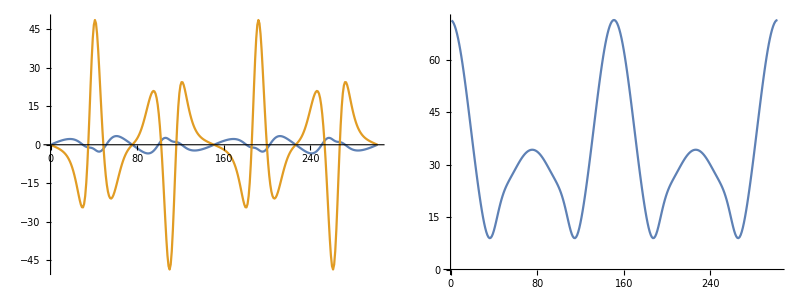

```mathematica
nsN=302;(*{etabsol1,eRsol1,eZsol1}={1.0849,{0.0,-0.014022},{0.0,-0.02}};*)
sol=objFuncAx[etabsol,eRsol,eZsol,R0,NFP,nIts,tol,nLineS,sigmainit,sigma0,nsN,psi31init,psi32init,psi33init,psi34init];
Grid[{{ListLinePlot[{sol[[5]],sol[[8]]},PlotRange->All,AxesOrigin->{0,0}],ListLinePlot[{sol[[4]]},PlotRange->All,AxesOrigin->{0,0}]}}]
```

#### Obtain Axis

```mathematica
nphiR=Length[eRsol];nphiZ=Length[eZsol];
Rnew[phi_]=R0+Sum[eRsol[[n]] Cos[n NFP phi],{n,1,nphiR}];
Znew[phi_]=Sum[eZsol[[n]] Sin[n NFP phi],{n,1,nphiZ}];
closedCurvenew[phi_]={Rnew[phi]Cos[phi],Rnew[phi]Sin[phi],Znew[phi]};
FSsystem[phi_]=Chop[FrenetSerretSystem[closedCurvenew[phi],phi]];
```

#### Number of Rotations of the Normal Vector

```mathematica
quadrant=0;nNormal=0;diffQuadrant=0;qnew=0;printv="";nl="\n";
Table[normalx=FSsystem[t][[2,2,1]]*Cos[t]+FSsystem[t][[2,2,2]]*Sin[t];
normaly=FSsystem[t][[2,2,3]];
If[Abs[normalx]>Abs[normaly],If[normalx>0,qnew=2,qnew=4],If[normaly>0,qnew=1,qnew=3]];
If[quadrant==0,quadrant=qnew,diffQuadrant=qnew-quadrant;];
If[Abs[diffQuadrant]==3,diffQuadrant=diffQuadrant/3];nNormal=nNormal+diffQuadrant/2;quadrant=qnew;,{t,0,2*Pi,2*Pi/NFP/15}];
nNormal;
```

#### Find flux surface free functions

```mathematica
nsNew=Length[sol[[2,All]]];etai=0.5;
eta=Table[etai=η/.FindRoot[Cosh[η]-(1+sol[[2,i]]^2+etabsol^4/(First[FSsystem[(2π)/nsNew i]][[1]])^4)(First[FSsystem[(2π)/nsNew i]][[1]])^2/(2 etabsol^2),{η,etai}];etai,{i,1,nsNew}];
delta=Table[δ/.FindRoot[Sin[2 (δ+NFP/2(2π)/nsNew i)]Sinh[eta[[i]]]-sol[[2,i]],{δ,-NFP/2(2π)/nsNew i}],{i,1,nsNew}];
mu=Tanh[eta];psi31=sol[[4]];psi32=sol[[5]];psi33=sol[[6]];psi34=sol[[7]];psi32V=sol[[8]];
```

#### Position vector of the surface - List

```mathematica
bnctemp=ParallelTable[fstemp=FSsystem[(2 π)/ns i][[2]];{fstemp[[2]],fstemp[[3]],closedCurvenew[(2 π)/nsNew i]},{i,1,nsNew}];
normal=bnctemp[[All,1]];binormal=bnctemp[[All,2]];closedCurveV=bnctemp[[All,3]];nstheta=200;
posvec[psi_]:=ParallelTable[
phi=(2 π)/nsNew i;theta=(2 π)/nstheta j;
psi2=(1+mu[[i]] Cos[2 (theta+delta[[i]])])/(√(1-mu[[i]]^2));
psi3=psi31[[i]]Cos[theta]+psi32[[i]]Sin[theta]+psi33[[i]]Cos[3theta]+psi34[[i]]Sin[3theta];
(*rho=Sqrt[psi/psi2]- psi psi3/(2 psi2^2)+(psi^(3/2) 5  psi3^2)/(8 psi2^(7/2))-(psi^2   psi3^3)/psi2^5+(psi^(5/2)231 psi3^4)/(128 psi2^(13/2)) ;*)
rho=ρ/.NSolve[{psi2 ρ^2+ psi3 ρ^3-psi==0,ρ>0},ρ,Reals][[1]]//Quiet;
closedCurveV[[i]]+rho(Cos[theta]normal[[i]]+Sin[theta]binormal[[i]])
,{i,1,nsNew},{j,1,nstheta}];
```

#### Position vector of the surface - Function

```mathematica
muFunc=ListInterpolation[mu,{0,2π},Method->"Spline",InterpolationOrder->1];
deltaFunc=ListInterpolation[delta,{0,2π},Method->"Spline",InterpolationOrder->1];
psi31Func=ListInterpolation[psi31,{0,2π},Method->"Spline",InterpolationOrder->1];
psi32Func=ListInterpolation[psi32,{0,2π},Method->"Spline",InterpolationOrder->1];
psi33Func=ListInterpolation[psi33,{0,2π},Method->"Spline",InterpolationOrder->1];
psi34Func=ListInterpolation[psi34,{0,2π},Method->"Spline",InterpolationOrder->1];
normFunc[ϕ_]=Re[Simplify[FSsystem[ϕ][[2,2]]]//Chop];
binormFunc[ϕ_]=Re[Simplify[FSsystem[ϕ][[2,3]]]//Chop];
psi2Func[ϕ_,θ_]=(1+muFunc[ϕ] Cos[2(θ+deltaFunc[ϕ])])/(√(1-muFunc[ϕ]^2));
psi3Func[ϕ_,θ_]=psi31Func[ϕ]Cos[θ]+psi32Func[ϕ]Sin[θ]+psi33Func[ϕ]Cos[3θ]+psi34Func[ϕ]Sin[3θ];
rhoFuncTemp[ϕ_,θ_,ψ_]=(√ψ)/(√psi2Func[ϕ,θ])-(ψ  psi3Func[ϕ,θ])/(2 psi2Func[ϕ,θ]^2)+(ψ^(3/2) 5  psi3Func[ϕ,θ]^2)/(8 psi2Func[ϕ,θ]^(7/2))-(ψ^2   psi3Func[ϕ,θ]^3)/psi2Func[ϕ,θ]^5+(ψ^(5/2)231 psi3Func[ϕ,θ]^4)/(128 psi2Func[ϕ,θ]^(13/2));
rhoFunc[ϕ_,θ_,ψ_]:=ρ/.NSolve[{psi2Func[ϕ,θ] ρ^2+psi3Func[ϕ,θ] ρ^3-ψ==0,ρ>0},ρ,Reals][[1]];
(*rhoFunc[ϕ_,θ_,ψ_]:=rhoFuncTemp[ϕ,θ,ψ];*)
posvecFunc[ϕ_,θ_,ψ_]:=closedCurvenew[ϕ]+rhoFunc[ϕ,θ,ψ](normFunc[ϕ]Cos[θ]+binormFunc[ϕ]Sin[θ]);
Rposvec[ϕ_,θ_,ψ_]:=posvecFunc[ϕ,θ,ψ][[1]]Cos[ϕ]+posvecFunc[ϕ,θ,ψ][[2]]Sin[ϕ];
Zposvec[ϕ_,θ_,ψ_]:=posvecFunc[ϕ,θ,ψ][[3]];
```

#### PlotResults

```mathematica
Show[ListPointPlot3D[posvec[0.001],PlotStyle->Directive[Gray]],ListPointPlot3D[closedCurveV,PlotStyle->Directive[Black,PointSize[0.008]]],ImageSize->Large]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot[{Rposvec[ϕ,θ,ψ],Zposvec[ϕ,θ,ψ]},{θ,0,2π},PlotRange->All,AspectRatio->Automatic]
,{ϕ,0,2π},{ψ,0.001,0.01}]
```

```mathematica
plot3D=ParametricPlot3D[posvecFunc[ϕ,θ,0.01],{ϕ,0,2π},{θ,0,2π},PlotPoints->{50,30},MaxRecursion->2,Mesh->None,ImageSize->Large,Axes->False,Boxed->False]
Export["/Users/rogeriojorge/Dropbox/senac/quasisymmetry/HighOrderQSmath.png",plot3D];
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-